## зад. 1 Дадена е функцията f(x)=sinx. Намерете полином, който да интерполира функцията при x0=0, x1=π/6, x2=π/3, като използвате функцията InterpolatingPolynomial.

## зад. 2 Изведете двустъпковите, тристъпковите и четиристъпковите формули на Адамс-Башфорт и Адамс-Мултон.

```mathematica
pb2[t_]=InterpolatingPolynomial[{{ti-h,fiMinus1},{ti,fi}},t];
Simplify[Integrate[p2[t],{t,ti,ti+h}]]
```

1/2 (3 fi-fiMinus1) h

```mathematica
pb3[t_]=InterpolatingPolynomial[{{ti-2*h,fiMinus2},{ti-h,fiMinus1},{ti,fi}},t];
Simplify[Integrate[p3[t],{t,ti,ti+h}]]
```

1/12 (23 fi-16 fiMinus1+5 fiMinus2) h

```mathematica
pb4[t_]=InterpolatingPolynomial[{{ti-3*h,fiMinus3},{ti-2*h,fiMinus2},{ti-h,fiMinus1},{ti,fi}},t];
Simplify[Integrate[p4[t],{t,ti,ti+h}]]
```

1/24 (55 fi-59 fiMinus1+37 fiMinus2-9 fiMinus3) h

```mathematica
pm2[t_] = InterpolatingPolynomial[{{ti+h,fiPlus1}, {ti,fi}},t];
Simplify[Integrate[pm2[t],{t,ti,ti+h}]]
```

1/2 (fi+fiPlus1) h

```mathematica
pm3[t_] = InterpolatingPolynomial[{{ti+h,fiPlus1}, {ti,fi}, {ti-h, fiMinus1}},t];
Simplify[Integrate[pm3[t],{t,ti,ti+h}]]
```

1/12 (8 fi-fiMinus1+5 fiPlus1) h

```mathematica
pm4[t_] = InterpolatingPolynomial[{{ti+h,fiPlus1}, {ti,fi}, {ti-h, fiMinus1}, {ti-2*h,fiMinus2}},t];
Simplify[Integrate[pm4[t],{t,ti,ti+h}]]
```

1/24 (19 fi-5 fiMinus1+fiMinus2+9 fiPlus1) h

## 3 зад. Имплементирайте четиристъпковия метод на Адамс-Башфорт и го приложете за решаване на задачата на Коши: du/dt=10u(1-u), 0<t≤6 u(0)=0.1 Изобразете точното и приближеното решение на една графика при h=0.1, 0.01, 0.001. Определете модул от абсолютните грешки при същите стойности. Имплементирайте и неявния метод на Адамс-Мултон. Приложете го за същата задача.

```mathematica
(*Метод на Рунге-Кута от четвърти ред*)
RK4[f_, t0_, T_, u0_, h_] := (
  n = Ceiling[(T - t0)/h];
  tArr = Table[t0 + i*h, {i, 0, n}];
  yArr = Table[0, {i, 0, n}];
  yArr[[1]] = u0;

  
  For[i = 1, i ≤ n, i++,
   k1 = h*f[tArr[[i]], yArr[[i]]];
   k2 = h*f[tArr[[i]] + h/2, yArr[[i]] + k1/2];
   k3 = h*f[tArr[[i]] + h/2, yArr[[i]] + k2/2];
   k4 = h*f[tArr[[i]] + h, yArr[[i]] + k3];
   yArr[[i + 1]] = yArr[[i]] + 1/6*(k1 + 2*k2 + 2*k3 + k4);
   ];
  Transpose[{tArr, yArr}]
  )
```

```mathematica
F[t_,u_] := 10*u*(1-u);
```

```mathematica
AB4[f_, t0_, T_, u0_, h_] :=
(
n = Ceiling[(T - t0)/h];
  tArr = Table[t0 + i*h, {i, 0, n}];
     yArr = Table[0, {i, 0, n}];
      yArr[[1]] = u0;

  
  For[i = 1, i ≤ 3, i++,
   k1 = h*f[tArr[[i]], yArr[[i]]];
   k2 = h*f[tArr[[i]] + h/2, yArr[[i]] + k1/2];
   k3 = h*f[tArr[[i]] + h/2, yArr[[i]] + k2/2];
   k4 = h*f[tArr[[i]] + h, yArr[[i]] + k3];
   yArr[[i + 1]] = yArr[[i]] + 1/6*(k1 + 2*k2 + 2*k3 + k4);
   ];
  FArr = {F[tArr[[1]],yArr[[1]]],F[tArr[[2]],yArr[[2]]],F[tArr[[3]],yArr[[3]]],F[tArr[[4]],yArr[[4]]]};
  For[i = 4, i ≤ n, i++,
   yArr[[i+1]] =yArr[[i]]+ 1/24 (55 FArr[[i]]-59 FArr[[i-1]]+37 FArr[[i-2]]-9 FArr[[i-3]])* h;
AppendTo[FArr,F[tArr[[i+1]],yArr[[i+1]]]];
   ];
Transpose[{tArr, yArr}]
)
```

```mathematica
exact[t_] = DSolve[{u'[t] == 10*u[t]*(1-u[t]), u[0] == 0.1},u[t],t][[1,1,2]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

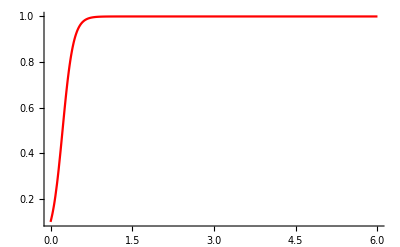

```mathematica
exactRes = Plot[exact[t],{t,0,6}, PlotRange->All, PlotStyle-> Red]
```

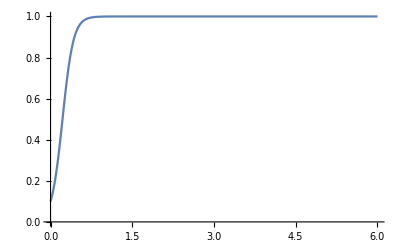

```mathematica
appr1 = ListLinePlot[AB4[F,0,6,0.1,0.01], PlotRange->All]
```

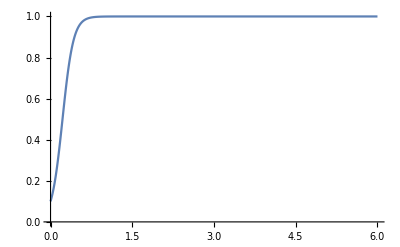

```mathematica
appr2 = ListLinePlot[AB4[F,0,6,0.1,0.001], PlotRange->All]
```

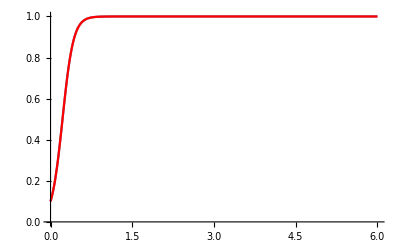

```mathematica
Show[appr1,exactRes]
```

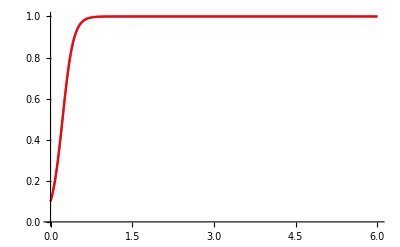

```mathematica
Show[appr2,exactRes]
```

```mathematica
err = Abs[exact[appr1[[All,1]]]-appr1[[All,2]]];
```

ListPlot::lpn: Abs[2.71828^10./(9.+2.71828^10.)-1. ] is not a list of numbers or pairs of numbers.

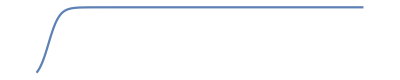
ListPlot[Abs[ⅇ^(10 -Graphics-)/(9.+ⅇ^(10 -Graphics-))--Graphics-],PlotRange→All]

```mathematica
ListPlot[err,PlotRange->All]
```